## B - spline

```mathematica
Subscript[P, 0] = {{0},{0}};
(*Subscript[P, 1] = {{0.5},{0.5}};*)
Subscript[P, 1]= {Sqrt[(0-1)^2]/2,Sqrt[(0-53)^2]/2}; (* sta a metà tra P0 e P2*)
Subscript[P, 2] = {{1},{53}};
Subscript[Q, 0] = Subscript[P, 2];
Subscript[Q, 2]= {{80},{-32}};
```

### Parametrico

```mathematica
(*definiamo i punti in modo parametrico*)
```

```mathematica
Subscript[P, i_] := {{Subscript[a, i]},{Subscript[b, i]}}
```

```mathematica
Subscript[Q, i_] := {{Subscript[c, i]},{Subscript[d, i]}}
```

```mathematica
Subscript[P, 1]
```

{{a_1},{b_1}}

```mathematica
Subscript[P, 2]
```

{{a_2},{b_2}}

```mathematica
(* prima curva di bezier*)
```

```mathematica
Subscript[B, 1]= Binomial[2,0]*Subscript[P, 0]*(1-l)^2*l^0+Binomial[2,1]*Subscript[P, 1]*(1-l)^1*l^1+Binomial[2,2]*Subscript[P, 2]*(1-l)^0*l^2
```

{{(1-l)^2 a_0+2 (1-l) l a_1+l^2 a_2},{(1-l)^2 b_0+2 (1-l) l b_1+l^2 b_2}}

```mathematica
(* seconda curva di bezier*)
```

```mathematica
Subscript[B, 2]= Binomial[2,0]*Subscript[Q, 0]*(1-l)^2*l^0+Binomial[2,1]*Subscript[Q, 1]*(1-l)^1*l^1+Binomial[2,2]*Subscript[Q, 2]*(1-l)^0*l^2
```

{{(1-l)^2 c_0+2 (1-l) l c_1+l^2 c_2},{(1-l)^2 d_0+2 (1-l) l d_1+l^2 d_2}}

```mathematica
(* deriviamo per imporre la continuità*)
```

```mathematica
Subscript[dB, 1] = D[Subscript[B, 1],l]
```

{{-2 (1-l) a_0+2 (1-l) a_1-2 l a_1+2 l a_2},{-2 (1-l) b_0+2 (1-l) b_1-2 l b_1+2 l b_2}}

```mathematica
Subscript[dB, 2] = D[Subscript[B, 2],l]
```

{{-2 (1-l) c_0+2 (1-l) c_1-2 l c_1+2 l c_2},{-2 (1-l) d_0+2 (1-l) d_1-2 l d_1+2 l d_2}}

```mathematica
(*Flatten mette in un unico vettore*)
(*ci mettiamo alla fine di B1 e all'inizio di B2*)
```

```mathematica
eq = Flatten[(Subscript[dB, 1]/.l-> 1)] - Flatten[(Subscript[dB, 2]/.l-> 0) ]
```

{-2 a_1+2 a_2+2 c_0-2 c_1,-2 b_1+2 b_2+2 d_0-2 d_1}

```mathematica
(*imponiamo che le derivate siano uguali imponendo la loro differenza pari a zero*)
```

```mathematica
sol = Solve[eq == 0] (*troviamo i punti di controllo della curva successivo*)
```

{{c_1→-a_1+a_2+c_0,d_1→-b_1+b_2+d_0}}

```mathematica
Subscript[curva, 1] = Subscript[B, 1]
```

{{(1-l)^2 a_0+2 (1-l) l a_1+l^2 a_2},{(1-l)^2 b_0+2 (1-l) l b_1+l^2 b_2}}

```mathematica
Subscript[curva, 2] = Subscript[B, 2]/.sol
```

{{{(1-l)^2 c_0+2 (1-l) l (-a_1+a_2+c_0)+l^2 c_2},{(1-l)^2 d_0+2 (1-l) l (-b_1+b_2+d_0)+l^2 d_2}}}

```mathematica
(Subscript[B, 1]) // MatrixForm
```

((1-l)^2 a_0+2 (1-l) l a_1+l^2 a_2
(1-l)^2 b_0+2 (1-l) l b_1+l^2 b_2)

```mathematica
(Subscript[B, 2]) // MatrixForm
```

((1-l)^2 c_0+2 (1-l) l c_1+l^2 c_2
(1-l)^2 d_0+2 (1-l) l d_1+l^2 d_2)

```mathematica
Subscript[Q, 1]/.sol (*puoi inserire valori numerici e trovi c e d*)
```

{{{-a_1+a_2+c_0},{-b_1+b_2+d_0}}}

### Grafico (valori numerici)

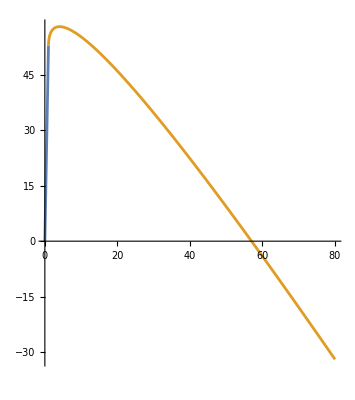

```mathematica
f[l_]:={{1. (1-l) l+l^2},{1. (1-l) l+2 l^2}};
f[l_] := Subscript[curva, 1]
f1[l_] := Subscript[curva, 2]
ParametricPlot[{f[l],f1[l]},{l,0,1}]
```